```mathematica
Get[NotebookDirectory[] <> \"metoda_MonteCarlo.m\"]
```

Približna vrednost π: SimulacijaMonteCarlo[10000.]

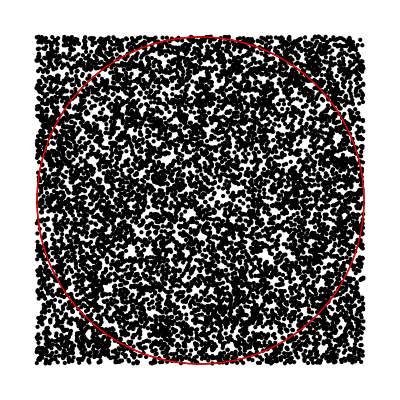

```mathematica
(*Monte Carlo*)
n=10000; (*Število simuliranih točk*)
priblPi=SimulacijaMonteCarlo[n];

(*približna vrednost π*)
Print["Približna vrednost π: ",N[priblPi]]

Graphics[{Circle[],PointSize[Small],Point[RandomReal[{-1,1},{n,2}]],Red,Circle[{0,0},1]}]

N[]
```

```mathematica
(* 1.2 Razvoj v vrsto in funkcija Manipulate *)
f[t_]:=Sin[t]*t^2*Exp[-t]
t0=2;
max=10; (*Največji red približka*)

taylorSeries[n_]:=Normal[Series[f[t],{t,t0,n}]]
```

```mathematica
approx[t_]:=Normal[Series[f[t],{t,2,4}]]
```

```mathematica
Manipulate[Plot[{f[t],Evaluate[taylorSeries[n]]},{t,0,4},PlotRange->All,PlotStyle->{Blue,Red},AxesLabel->{"t","f(t)"},ImageSize->Medium],{{n,1,"Red približka"},1,max,1}]
```